```mathematica
{1, 3, 4}
```

{1,3,4}

```mathematica
{1, a, cat}
```

```mathematica
mylist={1,a,cat}
```

{1,a,cat}

```mathematica
mylist+1
```

{2,1+a,1+cat}

```mathematica
Range[3,8]
```

{3,4,5,6,7,8}

```mathematica
mylist[[3]]
```

```mathematica
cat+1
```

1+cat

```mathematica
Table[j, {j,1,8,0.2}]
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.}

```mathematica
dicerolls=RandomInteger[{1,6},10000000];
```

```mathematica
1.0*Mean[dicerolls]
```

3.4999

```mathematica
squares=Table[i^2,{i,1,8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
upto8=Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
Map[#^2 &, upto8]
```

```mathematica
Map[Sqrt[#] &,{1,4,9,16,25,36,49,64}]
```

{1,2,3,4,5,6,7,8}

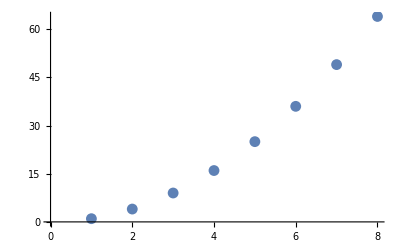

```mathematica
ListPlot[squares]
```

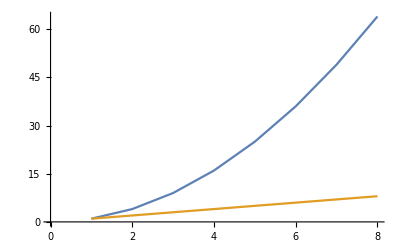

```mathematica
ListPlot[{squares,upto8}, Joined -> True]
```

```mathematica
Length[squares]
```

8

```mathematica
NestList[f,a,5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}

```mathematica
NestList[#*2 &,1,5]
```

{1,2,4,8,16,32}

```mathematica
NestWhileList[#*2 &,1,#≤123 &]
```

{1,2,4,8,16,32,64,128}

```mathematica
{1,2,3}+{a,b,c}
```

{1+a,2+b,3+c}

```mathematica
Union[{1,2,3},{3,4}]
```

{1,2,3,4}

```mathematica
Intersection[{1,2,3},{3,4}]
```

{3}

```mathematica
Subsets[{1,2,3}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Join[{1,2},{2,1}]
```

{1,2,2,1}

```mathematica
Riffle[{1,2},{a,b}]
```

{1,a,2,b}

```mathematica
Range[10]
```

```mathematica
Take[{1,2,3,4,5,6,7,8,9,10},3]
```

{1,2,3}

```mathematica
Drop[{1,2,3,4,5,6,7,8,9,10},3]
```

{4,5,6,7,8,9,10}

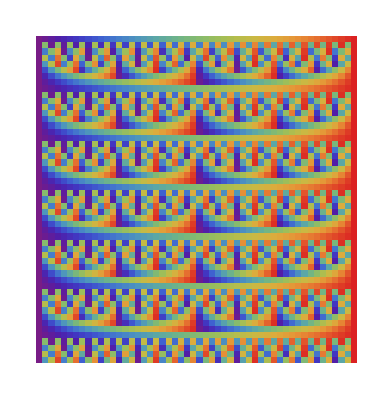

```mathematica
ArrayPlot[NestList[Riffle[Take[#,26],Drop[#,26]] &,Range[52], 52],ColorFunction->"Rainbow"]
```

```mathematica
MatrixForm[{{1,2},{3,4}}]
```

(1 | 2
3 | 4)

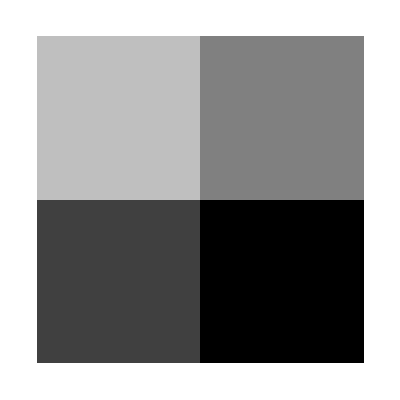

```mathematica
ArrayPlot[{{1,2},{3,4}}]
```

```mathematica
Sqrt[4]
```

2

```mathematica
timestwoadd[x_]:=2*x + 1
```

```mathematica
timestwoadd[12]
```

25

```mathematica
fn := #*2 + 1 &
```

```mathematica
fn[12]
```

25

```mathematica
testifinputis7[wat_]:=If[wat==7,1,0]
```

```mathematica
testifinputis7[6.99]
```

0

```mathematica
testifinputis7[7.1]
```

0

```mathematica
testifinputis7[7]
```

1

```mathematica
Map[testifinputis7,Range[10]]
```

{0,0,0,0,0,0,1,0,0,0}

```mathematica
If[4>2,1,0]
```

1

```mathematica
Map[Mod[#,5] &,Range[30]]
```

{1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0,1,2,3,4,0}

```mathematica
collatz[x_,y_]:=If[x==3*y||x==2*y+1||y==3*x||y==2*x+1,1,0]
```

```mathematica
Array[# &,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Array[# &,{4,4}]
```

{{1,1,1,1},{2,2,2,2},{3,3,3,3},{4,4,4,4}}

```mathematica
Array[#1+2#2&,{4,4}]
```

{{3,5,7,9},{4,6,8,10},{5,7,9,11},{6,8,10,12}}

```mathematica
GraphPlot3D[AdjacencyGraph[Array[collatz[#1,#2]&,{150,150}]]]
```

-Graphics3D-

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
Map[#[[1]] &,Position[Map[Mod[#,7] &,Range[100]],6]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97}

```mathematica
Flatten[{{1,2},{3,4}}]
```

{1,2,3,4}

```mathematica
Select[Table[i,{i,1,10}],Mod[#,3]==0&]
```

{3,6,9}

```mathematica
Sort[RandomReal[{0,1},7],#1≥#2 &]
```

{0.874683,0.835146,0.764212,0.752976,0.553839,0.154525,0.0782879}

```mathematica
"mystring"
```

mystring

```mathematica
StringJoin["glaba","blaga"]
```

glabablaga

```mathematica
StringJoin["Next is true.","Back is false."]
```

Next is true.Back is false.

```mathematica
ToString[{{1,2},{3,4}}]
```

{{1, 2}, {3, 4}}

```mathematica
ToExpression["{{1, 2}, {3, 4}}"]
```

{{1,2},{3,4}}

```mathematica
StringSplit["{3,1,2,3,4,1,2,3}","1"]
```

{{3,,,2,3,4,,,2,3}}

```mathematica
StringReplace["{3,4,12,3,4,1,2,3,1,1,2,3,4,1}","1"->"10"]
```

{3,4,102,3,4,10,2,3,10,10,2,3,4,10}

```mathematica
Characters["catfish"]
```

{c,a,t,f,i,s,h}

```mathematica
NestList[StringReplace[#,"110"->"10000011101"] &,"110110110",5]
```

{110110110,100000111011000001110110000011101,1000001100000111011000001110100001100000111011000001110100001100000111011,100000100000111010000110000011101100000111010000110000011101100001000001110100001100000111011000001110100001100000111011000010000011101000011000001110111,10000010000011000001110110000100000111010000110000011101100000111010000110000011101100001000001110100001100000111011000001110100010000011000001110110000100000111010000110000011101100000111010000110000011101100001000001110100001100000111011000001110100010000011000001110110000100000111010000110000011101111,100000100000100000111010000110000011101100000111010001000001100000111011000010000011101000011000001110110000011101000011000001110110000100000111010000110000011101100000111010001000001100000111011000010000011101000011000001110110000011101000011000001110110001000001000001110100001100000111011000001110100010000011000001110110000100000111010000110000011101100000111010000110000011101100001000001110100001100000111011000001110100010000011000001110110000100000111010000110000011101100000111010000110000011101100010000010000011101000011000001110110000011101000100000110000011101100001000001110100001100000111011111}

```mathematica
conv[x_]:=Map[If[#=="0",1,2]&,Characters[x]]
```

```mathematica
conv["110110110"]
```

{2,2,1,2,2,1,2,2,1}

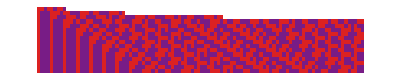

```mathematica
ArrayPlot[Map[Take[conv[#],Min[100,StringLength[#]]] &,NestList[StringReplace[#,"110"->"100011101"]&,"110110110",15]],ColorFunction->"Rainbow"]
```

```mathematica
cat=7
```

7

```mathematica
cat
```

7

```mathematica
a=3+2ⅈ
b=√2
c=ⅇ^1.5
d=(1+√2)/2
a+b+c+d
```

3+2 ⅈ

√2

4.48169

1/2 (1+√2)

10.103+2. ⅈ

```mathematica
%+2
```

12.103+2. ⅈ

```mathematica
y=x^2
```

x^2

```mathematica
x^2+Sin[x]/.x->y^2+z
```

(x^4+z)^2+Sin[x^4+z]

# Understanding Mathematica

```mathematica
TrigToExp[Sin[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

```mathematica
ExpToTrig[Exp[x]]
```

Cosh[x]+Sinh[x]

```mathematica
Expand[(x+1)(x-1)]
```

-1+x^2

```mathematica
Simplify[x^2+(2 x^2+sin[x])]
```

3 x^2+sin[x]

```mathematica
Factor[x^2-1]
```

(-1+x) (1+x)

```mathematica
N[π,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
poly=1+3 x^2+5 x^3+6Sin[x]
```

1+3 x^2+5 x^3+6 Sin[x]

```mathematica
Coefficient[poly,x^2]
```

3

```mathematica
Solve[z==x^2+1,x]
```

{{x→-√(-1+z)},{x→√(-1+z)}}

```mathematica
x/.{{x->-√(-1+z)},{x->√(-1+z)}}
```

{-√(-1+z),√(-1+z)}

```mathematica
Solve[x+y+z==1 && x-y==2,{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-2+x,z→3-2 x}}

```mathematica
z=3+2ⅈ
```

3+2 ⅈ

```mathematica
z^2
```

5+12 ⅈ

```mathematica
Re[z]
```

3

```mathematica
Arg[z]
```

ArcTan[2/3]

```mathematica
A={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
v={v1,v2}
```

{v1,v2}

```mathematica
A//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
A.v
% //MatrixForm
```

{v1+2 v2,3 v1+4 v2}

(v1+2 v2
3 v1+4 v2)

```mathematica
Det[A]
Inverse[A] //MatrixForm
MatrixPower[A,2] //MatrixForm
A^2 //MatrixForm
Transpose[A] //MatrixForm
Eigenvalues[A] //MatrixForm
KroneckerProduct[A,A] //MatrixForm
A[[1]] //MatrixForm
A[[2,2]]
```

-2

(-2 | 1
3/2 | -1/2)

(7 | 10
15 | 22)

(1 | 4
9 | 16)

(1 | 3
2 | 4)

(1/2 (5+√33)
1/2 (5-√33))

(1 | 2 | 2 | 4
3 | 4 | 6 | 8
3 | 6 | 4 | 8
9 | 12 | 12 | 16)

(1
2)

4

```mathematica
M=Table[i*j + Sin[i+j], {i,1,10}, {j,1,10}];
M //MatrixForm
```

(1+Sin[2] | 2+Sin[3] | 3+Sin[4] | 4+Sin[5] | 5+Sin[6] | 6+Sin[7] | 7+Sin[8] | 8+Sin[9] | 9+Sin[10] | 10+Sin[11]
2+Sin[3] | 4+Sin[4] | 6+Sin[5] | 8+Sin[6] | 10+Sin[7] | 12+Sin[8] | 14+Sin[9] | 16+Sin[10] | 18+Sin[11] | 20+Sin[12]
3+Sin[4] | 6+Sin[5] | 9+Sin[6] | 12+Sin[7] | 15+Sin[8] | 18+Sin[9] | 21+Sin[10] | 24+Sin[11] | 27+Sin[12] | 30+Sin[13]
4+Sin[5] | 8+Sin[6] | 12+Sin[7] | 16+Sin[8] | 20+Sin[9] | 24+Sin[10] | 28+Sin[11] | 32+Sin[12] | 36+Sin[13] | 40+Sin[14]
5+Sin[6] | 10+Sin[7] | 15+Sin[8] | 20+Sin[9] | 25+Sin[10] | 30+Sin[11] | 35+Sin[12] | 40+Sin[13] | 45+Sin[14] | 50+Sin[15]
6+Sin[7] | 12+Sin[8] | 18+Sin[9] | 24+Sin[10] | 30+Sin[11] | 36+Sin[12] | 42+Sin[13] | 48+Sin[14] | 54+Sin[15] | 60+Sin[16]
7+Sin[8] | 14+Sin[9] | 21+Sin[10] | 28+Sin[11] | 35+Sin[12] | 42+Sin[13] | 49+Sin[14] | 56+Sin[15] | 63+Sin[16] | 70+Sin[17]
8+Sin[9] | 16+Sin[10] | 24+Sin[11] | 32+Sin[12] | 40+Sin[13] | 48+Sin[14] | 56+Sin[15] | 64+Sin[16] | 72+Sin[17] | 80+Sin[18]
9+Sin[10] | 18+Sin[11] | 27+Sin[12] | 36+Sin[13] | 45+Sin[14] | 54+Sin[15] | 63+Sin[16] | 72+Sin[17] | 81+Sin[18] | 90+Sin[19]
10+Sin[11] | 20+Sin[12] | 30+Sin[13] | 40+Sin[14] | 50+Sin[15] | 60+Sin[16] | 70+Sin[17] | 80+Sin[18] | 90+Sin[19] | 100+Sin[20])

```mathematica
N[M]
```

{{1.9093,2.14112,2.2432,3.04108,4.72058,6.65699,7.98936,8.41212,8.45598,9.00001},{2.14112,3.2432,5.04108,7.72058,10.657,12.9894,14.4121,15.456,17.,19.4634},{2.2432,5.04108,8.72058,12.657,15.9894,18.4121,20.456,23.,26.4634,30.4202},{3.04108,7.72058,12.657,16.9894,20.4121,23.456,27.,31.4634,36.4202,40.9906},{4.72058,10.657,15.9894,20.4121,24.456,29.,34.4634,40.4202,45.9906,50.6503},{6.65699,12.9894,18.4121,23.456,29.,35.4634,42.4202,48.9906,54.6503,59.7121},{7.98936,14.4121,20.456,27.,34.4634,42.4202,49.9906,56.6503,62.7121,69.0386},{8.41212,15.456,23.,31.4634,40.4202,48.9906,56.6503,63.7121,71.0386,79.249},{8.45598,17.,26.4634,36.4202,45.9906,54.6503,62.7121,71.0386,80.249,90.1499},{9.00001,19.4634,30.4202,40.9906,50.6503,59.7121,69.0386,79.249,90.1499,100.913}}

```mathematica
f[x_]:=Cos[x]+Sin[x]
g[x_]:=Cos[x]-2
f[1]
N[f[1],5]
```

Cos[1]+Sin[1]

1.3818

```mathematica
h[x_,y_]:=Sin[x]+Cos[y]
h[1,2] //N
```

0.425324

So for using the sum, just use escape and brains. Then for the limits, use ctrl+_ and ctrl+% (without shift..)

```mathematica
data={1,2,3,4,5,6};
av1[v_]:=1/Length[v]∑_(i=1)^Length[v] v[[i]];
av2[v_]:=Total[v]/Length[v];
N[av1[data]]
N[av2[data]]
```

3.5

3.5

## Just testing how to use subsections

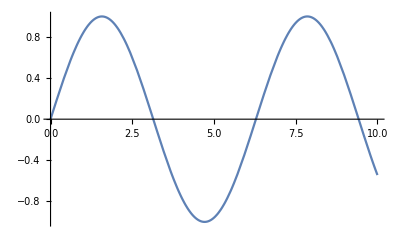

```mathematica
Plot[Sin[x],{x,0,10}]
```

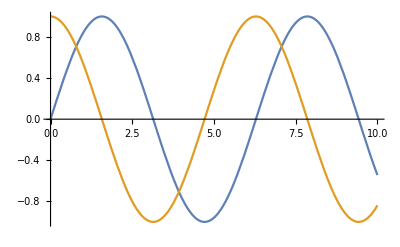

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,10}]
```

```mathematica
Plot3D[Sin[x]Cos[y],{x,0,5},{y,0,5}]
```

-Graphics3D-

We put the link here
https://www.youtube.com/watch?v=Zqkn8CoJp9k

```mathematica
ParametricPlot3D[{Cos[t],Sin[t],t},{t,0,4π}]
```

-Graphics3D-

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
Integrate[%,x]
```

Sin[x]

```mathematica
D[Cos[x]Sin[x],x]
```

Cos[x]^2-Sin[x]^2

```mathematica
Integrate[Cos[x]Sin[x],x]
```

-1/2 Cos[x]^2

```mathematica
DSolve[2y'[x]+3y[x]+Cos[x]==x,y[x],x]
```

{{y[x]→ⅇ^(-3 x/2) C[1]+1/117 (-26+39 x-27 Cos[x]-18 Sin[x])}}

```mathematica
DSolve[{y1'[x]==y2[x],y2'[x]+3==y1[x]},{y1[x],y2[x]},x]
```

{{y1[x]→-3/4 ⅇ^-x (-ⅇ^-x+ⅇ^x) (-1+ⅇ^(2 x))+3/4 ⅇ^(-2 x) (1+ⅇ^(2 x))^2+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2],y2[x]→-3/4 ⅇ^-x (-ⅇ^-x+ⅇ^x) (1+ⅇ^(2 x))+3/4 ⅇ^(-2 x) (-1+ⅇ^(2 x)) (1+ⅇ^(2 x))+1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]}}

```mathematica
Sum[i^2,{i,1,n}]
```

1/6 n (1+n) (1+2 n)

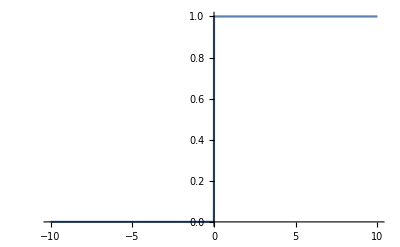

```mathematica
d[x_]:=If[x≥0,1,0]
Plot[d[x],{x,-10,10}]
```

```mathematica
a=0;
For[i=1,i≤10,i++,
a=a+i^2;
]
a
```

385

```mathematica
a=0;
total=0
While[a<10,
	a=a+1;
	total=total+a;
	Print[total];
]
```

0

1

3

6

10

15

21

28

36

45

55

```mathematica
Manipulate[Plot3D[Sin[a x]Cos[2a y],{x,0,5}, {y,0,5}],{a,0,2}]
```

There’s a built-in export command (just right click on the image (perhaps not he manipulated one above)) and there’s a copy as latex which you can use to export things as latex.

```mathematica
n=100;
p=0.5;
m=1000;

finalPosition=Table[0,{i,1,n}];

For[iter=1,iter≤m,iter++,
x=Floor[n/2];
For[t=1,t≤n/2-1,t++,
If[p>Random[],
x=x+1,
x=x-1
];
];
finalPosition[[x]]=finalPosition[[x]]+1;
];

finalPosition=finalPosition/iter;
ListLinePlot[finalPosition,PlotRange->All]
```

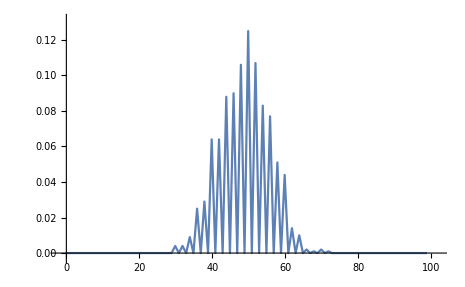

```mathematica
fib[n_]:=If[n≤2,1,fib[n-1]+fib[n-2]]
Table[fib[n],{n,1,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

Now this is some quantum optics stuff :D
I’m so excited, no more algebraic mistakes!! :)

```mathematica
inputState=a^2/(√(2!))b^2/(√(2!));
BSrule={a->(a+b)/(√2),b->(a-b)/(√2)};
toFockRule={a^n_-> √(n!)Ket[a,n],b^n_-> √(n!)Ket[b,n]};
inputState /. toFockRule
inputState /. BSrule
output=Expand[%] /. toFockRule
P04=Abs[Coefficient[output,Ket[a,4]]]^2
P22=Abs[Coefficient[output,Ket[a,2]Ket[b,2]]]^2
P40=Abs[Coefficient[output,Ket[b,]]]^2
P04+P22+P40
```

a,2 b,2

1/8 (a-b)^2 (a+b)^2

1/2 √(3/2) a,4-1/2 a,2 b,2+1/2 √(3/2) b,4

3/8

1/4

3/8

1